Click here to change glyph color->$CellContext`c

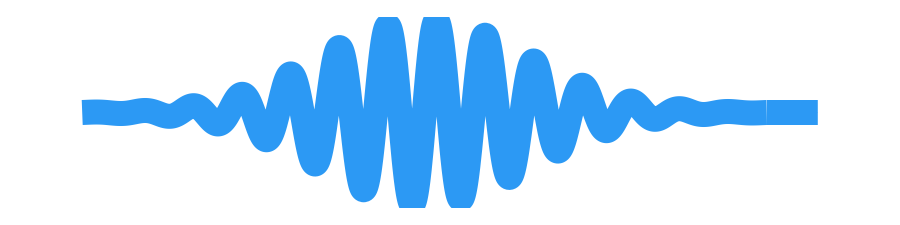

GammaRayGlyph.png

0.06666666666666667

```mathematica
SetDirectory[NotebookDirectory[]];
t=0.02;

Print["Click here to change glyph color->",ColorSetter[Dynamic[c]]]
gammaray=Magnify[Show[
Plot[y2+0.04*Sin[220*(x1-x2)]*Exp[-(x1-x2)^2/0.007],{x1,x2-0.2,x2+0.2},
PlotRange->All,PlotStyle->Directive[Thickness[t],c]],
Graphics[{c,Thickness[t],Arrowheads[0.1],Arrow[{{0.9,y/2},{0.93,y/2}}]}],
Axes->False,ImageSize->900,AspectRatio->1/4
],3.0]
Export["GammaRayGlyph.png",gammaray,Background->None]
```